# Groundstate Energy and Bond Length of Carbon Monoxide CO (including 3sσ spheroidal orbital)

```mathematica
SetDirectory[NotebookDirectory[]];
<<../fermifab.m;
<<diatomic_base.m;
fermifabML=Install["../mlink/fermifabML/Windows-x86-64/fermifabML"];
```

```mathematica
<<PhysicalConstants`
```

```mathematica
(* experimental bond length of CO, in atomic units *)
Subscript[R, CO]=112.8 10^-12 Meter/BohrRadius
```

2.13161

```mathematica
(* average nuclear charge of a carbon and oxygen atom *)
Subscript[Z, CO]=(6+8)/2
```

7

```mathematica
Subscript[R, CO] Subscript[Z, CO]
```

14.9213

```mathematica
(* nuclear charge difference *)
Subscript[ΔZ, CO]=8-6
```

2

```mathematica
(* quantum numbers *)
Subscript[m, l]=0;
Subscript[s, s]=0;
Subscript[m, s]=0;
```

```mathematica
paraInfo=ParaInfo[Subscript[ΔZ, CO]/Subscript[Z, CO]]⟦;;11⟧
```

{{1,0,0,{4/7,1/2},19},{1,1,0,{3/7,1/2},19},{2,0,0,{2/7,3/4},23},{2,1,0,{3/14,1},26},{1,2,0,{2/7,3/4},22},{1,1,1,{2/7,3/4},22},{1,1,-1,{2/7,3/4},22},{1,2,1,{3/14,5/4},25},{1,2,-1,{3/14,5/4},25},{1,3,0,{3/14,5/4},22},{3,0,0,{4/21,1},30}}

```mathematica
QuantNumbersToString[#⟦1;;3⟧]&/@paraInfo
```

{1sσ,1pσ,2sσ,2pσ,1dσ,1p(+π),1p(-π),1d(+π),1d(-π),1fσ,3sσ}

```mathematica
(* load precomputed integral tables *)
<<diatomic_coulomb_m0_zseries.m;
<<diatomic_coulomb_m1_zseries.m;
<<diatomic_coulomb_m2_zseries.m;
```

```mathematica
SymIntRule[ri_]:=Rule[First[ri],{First[ri],Outer[#+Transpose[#]&,Last[ri],2]}]
```

```mathematica
radinttables={SymIntRule/@radialIntM0TauZSeries,SymIntRule/@radialIntM1TauZSeries,SymIntRule/@radialIntM2TauZSeries};
```

## Calculate simultaneous LS eigenspaces

```mathematica
diatomicQuantLz=#⟦3⟧&/@paraInfo
```

{0,0,0,0,0,1,-1,1,-1,0,0}

```mathematica
DiatomicAngularMomentumZ[]:=KroneckerProduct[SparseArray[DiagonalMatrix[diatomicQuantLz⟦3;;-1⟧]],IdentityMatrix[2]]
```

```mathematica
DiatomicSpinUp[length_]:=KroneckerProduct[SparseArray[IdentityMatrix[length/2]],{{0,1},{0,0}}]
DiatomicSpinDown[length_]:=KroneckerProduct[SparseArray[IdentityMatrix[length/2]],{{0,0},{1,0}}]
DiatomicSpinZ[length_]:=KroneckerProduct[SparseArray[IdentityMatrix[length/2]],{{1/2,0},{0,-1/2}}]
DiatomicSpin[length_]:=Module[{Su=DiatomicSpinUp[length],Sd=DiatomicSpinDown[length],Sz=DiatomicSpinZ[length]},{(Su+Sd)/2,-ⅈ(Su-Sd)/2,Sz}]
```

```mathematica
diorbnames=Flatten[Outer[#1<>#2&,QuantNumbersToString[#⟦1;;3⟧]&/@paraInfo,{"↑","↓"}]]
Length[diorbnames]
```

{1sσ↑,1sσ↓,1pσ↑,1pσ↓,2sσ↑,2sσ↓,2pσ↑,2pσ↓,1dσ↑,1dσ↓,1p(+π)↑,1p(+π)↓,1p(-π)↑,1p(-π)↓,1d(+π)↑,1d(+π)↓,1d(-π)↑,1d(-π)↓,1fσ↑,1fσ↓,3sσ↑,3sσ↓}

22

```mathematica
2(Length[paraInfo]-2)
```

18

```mathematica
(* diatomic CO molecule *)
diLz=PurgeSparseArray[p2N[DiatomicAngularMomentumZ[],2(Length[paraInfo]-2),1,10(*valence electrons*)]];
diS=PurgeSparseArray[p2N[#,2(Length[paraInfo]-2),1,10]]&/@DiatomicSpin[2(Length[paraInfo]-2)];
diSS=PurgeSparseArray[Total[#.#&/@diS]];
```

```mathematica
(* check: diagonal matrix *)
PurgeSparseArray[diLz-DiagonalMatrix[Diagonal[diLz]]]
PurgeSparseArray[diS⟦3⟧-DiagonalMatrix[Diagonal[diS⟦3⟧]]]
```

SparseArray[<0>,{43758,43758}]

SparseArray[<0>,{43758,43758}]

```mathematica
(* indices of Subscript[L, z]-Subscript[S, z] eigevalues Subscript[m, l] and Subscript[m, s] *)
iZ=Intersection[Flatten[Position[Normal[Diagonal[diLz]],Subscript[m, l]]],Flatten[Position[Normal[Diagonal[diS⟦3⟧]],Subscript[m, s]]]];
Length[iZ]
```

4116

```mathematica
(* short test *)
diS⟦3⟧⟦First[iZ],First[iZ]⟧
```

0

```mathematica
(* parity not conserved, but we use it to order basis *)
diatomicParitySpatial=(-1)^(#⟦2⟧)&/@paraInfo
DiatomicParity[]:=Flatten[KroneckerProduct[diatomicParitySpatial⟦3;;-1⟧,{1,1}]]
Times@@(DiatomicParity[]⟦FermiToCoords[#]⟧)&/@FermiMap[2(Length[paraInfo]-2),10];
{iEven,iOdd}={Flatten[Position[%,1]],Flatten[Position[%,-1]]};
{Length[iEven],Length[iOdd]}
Length[DeleteDuplicates[Join[iEven,iOdd]]]
diSS⟦Join[iEven,iOdd],Join[iEven,iOdd]⟧
%⟦Length[iEven]+1;;-1,1;;Length[iEven]⟧//ArrayRules
```

{1,-1,1,-1,1,-1,-1,1,1,-1,1}

{21886,21872}

43758

SparseArray[<259848>,{43758,43758}]

{{_,_}→0}

```mathematica
iZeven=Intersection[iZ,iEven];
Length[iZeven]
simEven=NullSpace[diSS⟦iZeven,iZeven⟧];
Dimensions[simEven]
simEven=SparseArray[Orthogonalize[simEven]]
simEven=simEven.SparseArray[{i_,i_}->1,Binomial[2(Length[paraInfo]-2),10]{1,1}]⟦iZeven,All⟧;
Dimensions[simEven]
```

2064

{668,2064}

SparseArray[<6690>,{668,2064}]

{668,43758}

```mathematica
iZodd=Intersection[iZ,iOdd];
Length[iZodd]
simOdd=NullSpace[diSS⟦iZodd,iZodd⟧];
Dimensions[simOdd]
simOdd=SparseArray[Orthogonalize[simOdd]];
simOdd=simOdd.SparseArray[{i_,i_}->1,Binomial[2(Length[paraInfo]-2),10]{1,1}]⟦iZodd,All⟧;
Dimensions[simOdd]
```

2052

{648,2052}

{648,43758}

```mathematica
Put[Definition[simEven],Definition[simOdd],"carbon_monoxide_3sub_simLS.m"];
```

```mathematica
<<carbon_monoxide_3sub_simLS.m;
```

```mathematica
simLS=Join[simEven,simOdd]
```

SparseArray[<13106>,{1316,43758}]

```mathematica
(* show entries *)
Union[Last/@ArrayRules[simLS]]
```

{-1/2,-11/60,-1/6,-3/20,-2/15,-1/10,-1/12,0,1/60,1/20,1/15,1/10,7/60,3/20,1/6,2/5,5/12,1/2,1,-(√(2/7))/3,(√(2/7))/3,-(√(3/10))/2,(√(3/10))/2,-(√(2/5))/3,(√(2/5))/3,(2 √(2/5))/3,-(√(3/7))/4,(√(3/7))/4,-(√(3/5))/4,-(√(2/3))/5,-(√(5/6))/2,(√(5/6))/2,-(√(3/2))/10,(√(3/2))/10,-(√(5/3))/12,(√(5/3))/12,(√(5/3))/4,(√(5/3))/3,-1/(√2),-1/(3 √2),-1/(4 √2),-1/(6 √2),1/(12 √2),1/(6 √2),1/(3 √2),1/(2 √2),1/(√2),-(√2)/3,(√2)/3,-(√(5/2))/12,-1/(2 √3),-1/(4 √3),-1/(6 √3),1/(12 √3),1/(6 √3),1/(4 √3),1/(2 √3),1/(√3),(√3)/4,(√(7/2))/6,-1/(√5),-1/(2 √5),-1/(4 √5),1/(6 √5),1/(2 √5),1/(√5),-1/(5 √6),1/(10 √6),1/(5 √6),1/(√6),-1/(2 √10),-1/(3 √10),-1/(4 √10),-1/(6 √10),1/(12 √10),1/(6 √10),1/(4 √10),1/(3 √10),1/(2 √10),1/(√10),-5/(6 √14),-1/(2 √14),-1/(3 √14),-1/(6 √14),1/(6 √14),1/(3 √14),1/(2 √14),-7/(12 √15),-1/(2 √15),-1/(3 √15),-1/(4 √15),1/(6 √15),1/(4 √15),1/(3 √15),1/(2 √15),-1/(√21),-1/(2 √21),-1/(4 √21),1/(4 √21),1/(2 √21),1/(√21),5/(4 √21),-1/(√30),-1/(2 √30),1/(2 √30),1/(√30)}

```mathematica
(* check *)
Norm[PurgeSparseArray[simLS.Transpose[simLS]-SparseArray[{i_,i_}->1,Length[simLS]{1,1}]]]
Norm[PurgeSparseArray[diLz.Transpose[simLS]-Subscript[m, l] Transpose[simLS]]]
Norm[PurgeSparseArray[diS⟦3⟧.Transpose[simLS]-Subscript[m, s] Transpose[simLS]]]
Norm[PurgeSparseArray[diSS.Transpose[simLS]-Subscript[s, s](Subscript[s, s]+1)Transpose[simLS]]]
```

0

0

0

«1 more identical outputs»

```mathematica
FermiMap[{4,2(Length[paraInfo]-2)},{4,10}];
ψF=InterleaveFermi[#,%]&/@simLS;
Length[ψF]
```

1316

```mathematica
(* example *)
ψF⟦1⟧
FermiToCoords[Last[%⟦1⟧]]
SlaterToString[diorbnames,Last[ψF⟦1,1⟧]]
```

{{-1/(√2),4187151},{1/(√2),4184079}}

{1,2,3,4,11,14,15,16,17,18,19,20,21,22}

|1sσ↑ 1sσ↓ 1pσ↑ 1pσ↓ 1p(+π)↑ 1p(-π)↓ 1d(+π)↑ 1d(+π)↓ 1d(-π)↑ 1d(-π)↓ 1fσ↑ 1fσ↓ 3sσ↑ 3sσ↓⟩

## Calculate reduced 1- and 2-body density matrices

```mathematica
fm1=FermiMap[2Length[paraInfo],1];
fm2=FermiMap[2Length[paraInfo],2];
```

```mathematica
(*For[k=1,k≤Length[ψF],k++,Print[k];Put[SparseArray[Function[j,SymToSparseArray[RDM[ψF⟦j⟧,ψF⟦k⟧,1],IXI,fm1]]/@Range[Length[ψF]]],"carbon_monoxide_rho1_"<>ToString[k]<>".m"]];*)
```

```mathematica
(*For[k=1,k≤Length[ψF],k++,Print[k];Put[SparseArray[Function[j,SymToSparseArray[RDM[ψF⟦j⟧,ψF⟦k⟧,2],IXI,fm2]]/@Range[Length[ψF]]],"carbon_monoxide_rho2_"<>ToString[k]<>".m"]];*)
```

```mathematica
(*ρ1=SparseArray[{_,_}->0,{Length[ψF],Length[ψF],Length[fm1],Length[fm1]}]*)
```

```mathematica
(*For[i=1,i≤Length[ψF],i++,ρ1⟦i⟧=Get["carbon_monoxide_3sub_rho1/carbon_monoxide_rho1_"<>ToString[i]<>".m"]];*)
```

```mathematica
(*Put[Definition[ρ1],"carbon_monoxide_3sub_rho1.m"];*)
```

```mathematica
<<carbon_monoxide_3sub_rho1.m;
```

```mathematica
(*ρ1⟦11,2⟧//MatrixForm*)
```

```mathematica
(*ρ1⟦2,11⟧//MatrixForm*)
```

```mathematica
Tr[ρ1⟦-1,-1⟧]
```

14

```mathematica
(*ρ2=SparseArray[{_,_}->0,{Length[ψF],Length[ψF],Length[fm2],Length[fm2]}]*)
```

```mathematica
(*For[i=1,i≤Length[ψF],i++,Print[i];ρ2⟦i⟧=Get["carbon_monoxide_3sub_rho2/carbon_monoxide_rho2_"<>ToString[i]<>".m"]];*)
```

```mathematica
(*Put[Definition[ρ2],"carbon_monoxide_3sub_rho2.m"];*)
```

```mathematica
<<carbon_monoxide_3sub_rho2.m;
```

```mathematica
(*ρ2⟦1,1⟧//MatrixForm*)
```

```mathematica
Tr[ρ2⟦1,1⟧]
%-Binomial[14,2]
```

91

0

```mathematica
(*ρ2=SparseArray[Outer[SymToSparseArray[RDM[#2,#1,2],IXI,fm2]&,ψF,ψF,1]]*)
```

### Interleave Fermi states

```mathematica
(* Kronecker products of Fermi maps *)
fmKP1=Flatten[Outer[{##}&,fm1,fm1],1];
```

```mathematica
ρ1F=Outer[InterleaveFermi[Flatten[#],fmKP1]&,ρ1,2];
Dimensions[ρ1F]
```

{1316,1316}

```mathematica
(* Kronecker products of Fermi maps *)
fmKP2=Flatten[Outer[{##}&,fm2,fm2],1];
```

```mathematica
ρ2F=Outer[InterleaveFermi[Flatten[#],fmKP2]&,ρ2,2];
Dimensions[ρ2F]
```

{1316,1316}

### Trace out spin

```mathematica
ρr1=SparseArray[Outer[SymToSparseArray[SpinTraceSingle[#],SingInt,BosonMap[Length[paraInfo],1]]&,ρ1F,2]]
```

SparseArray[<49984>,{1316,1316,11,11}]

```mathematica
Put[Definition[ρr1],"carbon_monoxide_3sub_rhor1.m"];
```

```mathematica
(* example *)
ρr1⟦1,1⟧//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2)

```mathematica
Norm[(Tr[ρr1⟦#,#⟧]&/@Range[Length[ρr1]])-14]
```

0

```mathematica
diatomicQuantLz
```

{0,0,0,0,0,1,-1,1,-1,0,0}

```mathematica
CoulombSymmetry[a_,b_,c_,d_]:=CoulombSymmetry[c,d,a,b]/;a>c∨(a==c∧b>d)
CoulombSymmetry[a_,b_,c_,d_]:=CoulombSymmetry[b,a,d,c]/;a>b
CoulombSymmetry[a_,b_,c_,d_]:=Module[{qLz={0,0,0,0,0,1,-1,1,-1,0,0}},If[qLz⟦a⟧-qLz⟦b⟧==-(qLz⟦c⟧-qLz⟦d⟧),CoulInt[a,b,c,d],0]]
```

```mathematica
(* Coulomb operator with symbolic Coulomb integrals *)
ρr2=Outer[DiatomicSpinTraceCoulomb,ρ2F,2];
Dimensions[ρr2]
```

{1316,1316}

```mathematica
Put[Definition[ρr2],"carbon_monoxide_3sub_rhor2.m"];
```

```mathematica
(* example *)
ρr2⟦1,5⟧
```

-√2 CoulInt[1,1,5,11]+CoulInt[1,11,5,1]/(√2)-√2 CoulInt[2,2,5,11]+CoulInt[2,11,5,2]/(√2)+√2 CoulInt[5,6,6,11]-CoulInt[5,7,7,11]/(√2)+CoulInt[5,8,8,11]/(√2)+CoulInt[5,9,9,11]/(√2)+CoulInt[5,10,10,11]/(√2)-CoulInt[5,11,6,6]/(√2)-CoulInt[5,11,7,7]/(√2)-√2 CoulInt[5,11,8,8]-√2 CoulInt[5,11,9,9]-√2 CoulInt[5,11,10,10]-CoulInt[5,11,11,11]/(√2)

```mathematica
(* enumerate  all required Coulomb integrals *)
clist={};ρr2/.CoulInt[a_,b_,c_,d_]:>{clist=Union[clist,{{a,b,c,d}}];0};
Length[clist]
```

845

```mathematica
(* consistency check *)
(*Norm[Outer[((DiatomicSpinTraceCoulomb[#]/.CoulInt[a_,b_,c_,d_]:>CoulInt[CoordsToBoson[{a,b}],CoordsToBoson[{c,d}]])-SpinTraceCoulomb[#])/.CoulInt[a_,b_]:>CoulInt[b,a]/;b<a&,ρ2F,2]]*)
```

```mathematica
(* example *)
DiatomicSpinTraceCoulomb[ρ2F⟦1,2⟧]-DiatomicSpinTraceCoulomb[ρ2F⟦2,1⟧]
```

0

```mathematica
(* all unique Coulomb integrals after symmetry reduction *)
(*SparseArray[DeleteDuplicates[Select[Flatten[Table[CoulombSymmetry[a,b,c,d],{a,10},{b,10},{c,10},{d,10}]],#=!=0&]]/.CoulInt[a_,b_,c_,d_]:>Rule[{a,b,c,d},1],{10,10,10,10}]*)
```

## Calculate energies

```mathematica
(* example *)
(*Timing[couleval=EvalCoulInts[Subscript[ZR, CO],Subscript[ΔZR, CO],Subscript[R, CO],clist,radinttables]]
FullSimplify[ρr2⟦1,5⟧-ρr2⟦5,1⟧]
%/.CoulInt[a_,b_,c_,d_]:>couleval⟦a,b,c,d⟧*)
```

```mathematica
(* dependence on R *)
Rlist=Subscript[R, CO]+Range[-0.3,0.7,0.1]
```

{1.83161,1.93161,2.03161,2.13161,2.23161,2.33161,2.43161,2.53161,2.63161,2.73161,2.83161}

```mathematica
orbParamsList={#,OrbitalParameters[{2 Subscript[Z, CO],Subscript[ΔZ, CO]}#,paraInfo]}&/@Rlist;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
Vee=(Print["R: ",First[#]];Module[{couleval=EvaluateCoulombIntegrals[First[#],Last[#],clist,radinttables]},ρr2/.{CoulInt[a_,b_,c_,d_]:>couleval⟦a,b,c,d⟧}])&/@orbParamsList;
```

R: 1.83161

R: 1.93161

R: 2.03161

R: 2.13161

R: 2.23161

R: 2.33161

R: 2.43161

R: 2.53161

R: 2.63161

R: 2.73161

R: 2.83161

```mathematica
Dimensions[Vee]
```

{11,1316,1316}

```mathematica
Vee⟦3,1;;4,1;;4⟧
```

{{81.6,0.022566,0.0510707,0.0360756},{0.022566,86.1389,0.174286,0.00113725},{0.0510707,0.174286,82.9738,0.0033811},{0.0360756,0.00113725,0.0033811,92.1145}}

```mathematica
singleEnergy=EnergySingle[Subscript[Z, CO],{2 Subscript[Z, CO],Subscript[ΔZ, CO]}First[#],Last[#],ρr1]&/@orbParamsList;
```

```mathematica
(*ListPlot[Transpose[{Rlist,Min[Eigenvalues[#]]&/@singleEnergy}],Joined->True,Mesh->All]*)
```

```mathematica
(* Coulomb repulsion of the nuclei *)
{#,((Subscript[Z, CO]-Subscript[ΔZ, CO]/2)(Subscript[Z, CO]+Subscript[ΔZ, CO]/2))/#}&/@Rlist
Vnn=((Subscript[Z, CO]-Subscript[ΔZ, CO]/2)(Subscript[Z, CO]+Subscript[ΔZ, CO]/2))/# IdentityMatrix[Length[ρr1]]&/@Rlist;
```

{{1.83161,26.2064},{1.93161,24.8497},{2.03161,23.6266},{2.13161,22.5182},{2.23161,21.5091},{2.33161,20.5866},{2.43161,19.74},{2.53161,18.9603},{2.63161,18.2398},{2.73161,17.572},{2.83161,16.9515}}

```mathematica
minEnergyR=Transpose[{Rlist,Min[Eigenvalues[#]]&/@(singleEnergy+Vee+Vnn)}]
```

{{1.83161,-104.811},{1.93161,-105.004},{2.03161,-105.129},{2.13161,-105.198},{2.23161,-105.224},{2.33161,-105.22},{2.43161,-105.194},{2.53161,-105.155},{2.63161,-105.111},{2.73161,-105.066},{2.83161,-105.022}}

```mathematica
interpolEnergyR=Interpolation[minEnergyR]
```

InterpolatingFunction[{{1.83161,2.83161}},<>]

```mathematica
(* calculated minimum energy and bond length *)
FindMinimum[interpolEnergyR[R],{R,2.4}]
Emin={R/.Last[%],First[%]}
```

{-105.226,{R→2.26292}}

{2.26292,-105.226}

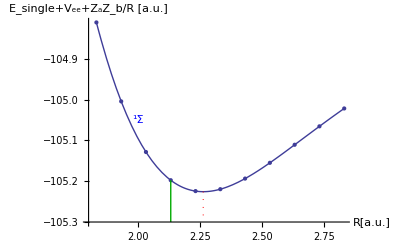

```mathematica
Show[Plot[interpolEnergyR[R],{R,First[Rlist],Last[Rlist]},AxesLabel->{"R[a.u.]","E_single+V_ee+Z_aZ_b/R [a.u.]"},AxesOrigin->{1.8,-105.3}],ListPlot[minEnergyR],Graphics[{Darker[Green],Line[{{Subscript[R, CO],-105.3},minEnergyR⟦Position[Rlist,Subscript[R, CO]]⟦1,1⟧⟧}]}],Graphics[{Dotted,Red,Line[{Emin,{First[Emin],-105.3}}]}],Graphics[Text[Style["^1Σ",Blue],{2,-105.05}]]]
```

```mathematica
(* minimum energy at experimental bond length *)
minEnergyR⟦Position[Rlist,Subscript[R, CO]]⟦1,1⟧⟧
```

{2.13161,-105.198}

```mathematica
(* eigenvalue gaps *)
First[Position[Rlist,Subscript[R, CO]]]
Differences[Eigenvalues[singleEnergy⟦%⟧+Vee⟦%⟧+Vnn⟦%⟧]⟦1;;6⟧]
```

{4}

{0.612087,0.3419,0.0760787,0.233726,0.132623}

### Bond dissociation energy

```mathematica
(* Explicit large nuclear charge limit of electronic ground states-Friesecke Goddard 2008 *)
−34.4468(* C atom *)-66.7048(* O atom *)
%-{Last[Emin],Last[minEnergyR⟦Position[Rlist,Subscript[R, CO]]⟦1,1⟧⟧]}
```

-101.152

{4.07409,4.04602}

```mathematica
(* 2 h c Ry *)
2PlanckConstant SpeedOfLight RydbergConstant/(ElectronCharge Volt)
eVToAU=First[%]
```

(27.2114 Joule)/(Coulomb Volt)

27.2114

```mathematica
(* experimental bond dissociation energy of CO ("Bond Dissociation Energies in Simple Molecules" by Darwent, 1970) *)
1071.94 10^3 1/(Mole AvogadroConstant) (Coulomb eV)/ElectronCharge
%/eVToAU au/eV
```

11.1099 eV

0.40828 au